```mathematica
smooth[x_]:=Sin[(π x)/2]^2
smoothe[x_]:=Sin[(π x)/2]
smoothb[x_]:=2  Sin[(π x)/4]^2
dsmooth[x_]:=π Cos[(π x)/2] Sin[(π x)/2]
dsmoothe[x_]:=1/2 π Cos[(π x)/2]
dsmoothb[x_]:=π Cos[(π x)/4] Sin[(π x)/4]
ismoothb[x_]:=x-(2 Sin[(x π)/2])/π
ismoothe[x_]:=(4 Sin[(π x)/4]^2)/π
ismooth[x_]:=1/2 (x-Sin[π x]/π)
```

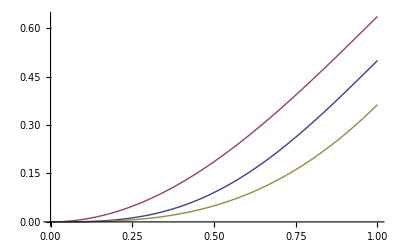

```mathematica
Plot[{ismooth@x,ismoothe@x,ismoothb@x},{x,0,1}]
```

```mathematica
Integrate[smooth@a,{a,0,x}]
```

1/2 (x-Sin[π x]/π)